# Predicting thermodynamic properties of Water/Steam with Predict and Heuristic Percepteron NetTrain on IAPWS/IF-97 data

## Aneet Dharmavaram Narendranath, PhD Michigan Technological University, Houghton, MI 49931 USA

Join the Conversation #WolframTechConf

## Brief Background of Presenter and Mathematica usage

### Where do I come from?

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

#### Microgravity film dynamics with NDSolve

```mathematica
Clear[x,t,xMin, xMax,TMax,frac,m,time];
xMin=0; xMax=2.Pi(Sqrt[2]/1);TMax =20;
   hsol=u /. NDSolve[{D[u[t, x], t] == -D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
        D[u[t, x]^3*D[u[t, x], x], x], u[0, x] == 1 - 0.1*Sin[1*(x/Sqrt[2])], 
    pbcs}, u, {t, 0, TMax}, {x, xMin, xMax}][[1]];
```

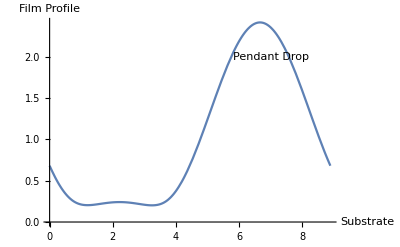

```mathematica
Plot[hsol[TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},Epilog->Inset[Framed[Style["Pendant Drop",12]],{7,2}]]
```

## Abstract of this talk

Pedagogically, the interpolation of specific enthalpy data may be treated as a decision making problem.  I utilize the Predict and NetTrain function for the specific enthalpy thermodynamic property of water based on the IAPWS IF-97 industrial standard.  Splitting the data into isobaric sets could be an important step. The gradient boosted decision trees method of predict performs better than a Naive percepteron approach. 

Specific enthalpies (h, kJ/kg) of steam as a function of pressure (P, bar) and temperature (T, Celsius) are imported.  In addition to the specific enthalpy, regions of water’s P-T phase diagram are also imported.  These regions are per the industrial standard IAPWS IF-97.  Mathematica’s Classify is used to check which numerical algorithm best classifies the (P,T) tuples into regions.  Classify provides an idea of dependence of specific enthalpy on temperature and pressure.  This algorithm is then used to create a prediction object for (P,T) → h which is then used to evaluate the power produced by a steam turbine, which is a fundamental building block in thermodynamics.  

A naive, heuristic percepteron is trained on isobaric data.

## Some Notes regarding treatment presented here

Treating this as a classification and Decision Tree problem allows for a high-level human orientated description of how zones of pressure and temperature are associated with different magnitudes of thermodynamic properties.  This may be exploited towards intuitive thermodynamic system design towards higher thermal efficiency or teaching ML/classification/NN to mechanical engineering students.

Treatment of evaluation of specific enthalpy using a decision tree model allows for intuitive move from steam tables to ML model.

There have been some other works on using ML for thermodynamics: Sencan (2006, 2011) [Performance of Ammonia/Water absorption refrigeration system], Yousefi (2017) [ANN to predict thermodynamic properties of pure and mixtures of alkali metals]

Previous work used equation of state described for entire region of P,T.  Coupled set of equations.

## Thermodynamics data

After using the Fisher Iris data set as a benchmark for classification and prediction accuracy, I turn my attention to a thermodynamic interpolated from IAPWS IF-97 industrial standard

```mathematica
url="http://pages.mtu.edu/~dnaneet/thermo/hptr_dense_1.txt";
(*url="http://pages.mtu.edu/~dnaneet/thermo/hptr.txt";*)
datasetDirty=Import[url, "Data"];
(*names={'celcius','bar','region','kJPerKg'}*)
s=Dimensions[datasetDirty][[1]];
dataset=Select[datasetDirty, #[[3]]≠ 0&]; (*Select only those rows and columns with non zero region*)
s=Dimensions[dataset][[1]];
```

```mathematica
s
Take[dataset,5]
```

36580

{{10,1,1,42.1174},{15,1,1,63.0778},{20,1,1,84.0118},{25,1,1,104.928},{30,1,1,125.833}}

## Division of data for easy training

#### Data division

```mathematica
T=dataset[[2;;Length[dataset],1]]; (*temperature, C*)
P=dataset[[2;;Length[dataset],2]]; (*pressure, bar*)
r=dataset[[2;;Length[dataset],3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"}; (*region, class/label*)
h=dataset[[2;;Length[dataset],4]]; (*specific enthalpy, kJ/kg*)
```

#### Clustering

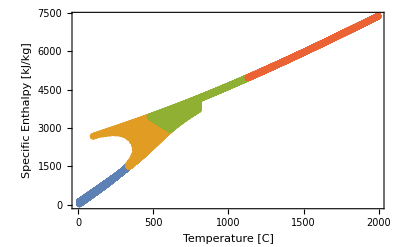

```mathematica
subset1=Thread[{T,h}];
c1=FindClusters[subset1,4,Method->"KMeans"];
ListPlot[c1,Frame->True,FrameStyle->Black,FrameLabel->{"Temperature [C]","Specific Enthalpy [kJ/kg]"},PlotStyle->{PointSize->0.012}]
```

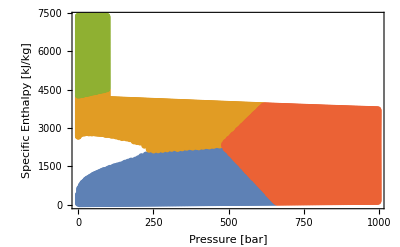

```mathematica
subset2=Thread[{P,h}];
c2=FindClusters[subset2,4,Method->"KMeans"];
ListPlot[c2,Frame->True,FrameStyle->Black,FrameLabel->{"Pressure [bar]","Specific Enthalpy [kJ/kg]"},PlotStyle->{PointSize->0.012}]
```

```mathematica
subset3d=Thread[{P,T,h}];
c3d=FindClusters[subset3d,4,Method->"KMeans"];
```

```mathematica
ListPlot3D[{c3d[[1]],c3d[[2]],c3d[[3]],c3d[[4]]},ImageSize->Large,Mesh->None]
```

-Graphics3D-

## Decision tree based Prediction Objects

Two Predict methods, viz., Decision tree and Gradient Boosted Trees are utilized to train the fit a sophisticated surface to the (P, T) -> h data

Empirically, a training set consisting of 95% of data allowed for the best prediction.  Anything less than 95% or greater than 95% led to less accuracy.

Since phase change shows discontinuous jump in specific enthalpy, the deviation from “actual” specific enthalpy at the point of phase change was used to make a decision on portion for training.

```mathematica
SeedRandom[1234];
thermoState=Thread[{T,P}]; (*thermodynamic state*)
mldata=RandomSample[Thread[thermoState->h]]; 
s=Dimensions[mldata][[1]];
training=mldata[[1;;Ceiling[0.95*s]]];
validation=mldata[[Ceiling[0.95*s]+1;;s]];
(*pThermo0=Predict[training,Method->"DecisionTree"]*)
pThermo1=Predict[training,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

## Prediction Quality

The nWorst predicted examples (ground truth) are :

```mathematica
Off[General::noinfo];
nWorst=300;
PredictorMeasurements[pThermo1,validation];
wpe1=%["WorstPredictedExamples"->nWorst];
(*wpe0=pm0["WorstPredictedExamples"->400];*)
Take[wpe1,10]
Dimensions[wpe1]
PredictorMeasurementsObject[…]
```

{{100,1}→2675.77,{205,16}→2803.57,{315,101}→2746.09,{290,76}→1289.66,{250,36}→2823.99,{330,141}→1521.47,{295,91}→1315.93,{345,146}→2675.26,{285,81}→1262.22,{335,126}→2726.84}

{300}

Percentage error Module

```mathematica
PercentageError[nWorst_,WorstPredExamples_, PredObject_]:=Module[{nw=nWorst, wpe=WorstPredExamples, pobj=PredObject},
statesBadPred=Table[wpe[[i]][[1]],{i,1,nw,1}];
d1=Dimensions[statesBadPred][[1]];
checkWithThese=Table[Select[wpe, #[[1]]==statesBadPred[[i]]&],{i,1,d1,1}];
Flatten[
Table[{checkWithThese[[i]][[1]][[2]]-pThermo1[statesBadPred[[i]]]}*100/ checkWithThese[[i]][[1]][[2]],{i,1,d1,1}]
]
]
```

Percentage error between ground truth and prediction

```mathematica
{Mean[Abs[PercentageError[Dimensions[wpe1][[1]],wpe1,pThermo1]]],StandardDeviation[Abs[PercentageError[Dimensions[wpe1][[1]],wpe1,pThermo1]]],Median[Abs[PercentageError[Dimensions[wpe1][[1]],wpe1,pThermo1]]]}
```

{2.32728,6.7861,0.827919}

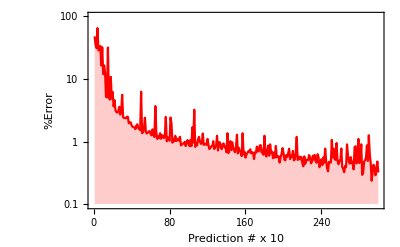

```mathematica
ListLogPlot[Abs[PercentageError[Dimensions[wpe1][[1]],wpe1,pThermo1]],GridLines->{None,{1,5}},GridLinesStyle->Directive[AbsoluteThickness[1.25],Blue],
Method->{"GridLinesInFront"->True},Frame->True,FrameStyle->Black,PlotStyle->{Red,PointSize->0.02},Joined->True,PlotRange->{All,{0,100}},FrameLabel->{"Prediction # x 10","%Error"},Filling->Axis]
```

## At what thermodynamic states does the model suffer from most error?

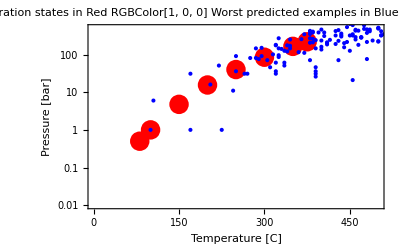

```mathematica
satState={{81,0.5},{100,1},{150,4.76 },{200,15.55},{250,40},{300,85},{350,165}, {375, 218.14}};
Show[{
ListLogPlot[satState,PlotRange->{{0.1,500},{0.01,500}},Frame->True,FrameStyle->Black,PlotStyle->{Red,PointSize->0.035},FrameLabel->{"Temperature [C]","Pressure [bar]"},PlotLabel->"Saturation states in Red RGBColor[1, 0, 0] \n Worst predicted examples in Blue RGBColor[0, 0, 1]",GridLines->{{373},{218}}],
ListLogPlot[{Take[statesBadPred,d1]},PlotStyle->{Blue,PointSize->0.3},FrameLabel->{"Temperature [C]","Pressure [bar]"}]
}]
```

## Prediction of Power produced by a Steam Turbine

The state of steam at the entrance and the exit to a reversible, adiabatic turbine is (T1, P1) = (320 °C, 5000 kPa) and (T2, P2) = (99.98 °C, 100 kPa).  If the changes in specific kinetic energy and specific potential energy are negligible in comparison to change in specific enthalpy, find the useful power generated by this turbine when operating at steady state.

```mathematica
{Tin, Pin} = {400, 51};
{Tout, Pout} = {100, 1};
{
(*hin=pThermo0[{Tin, Pin}],
hout=pThermo0[{Tout, Pout}],*)
hin=pThermo1[{Tin, Pin}],
hout=pThermo1[{Tout, Pout}]}
wout0 =Quantity[hin - hout,"kJ/kg"]
```

{3192.51,1401.32}

1791.19 kJ/kg

```mathematica
{Select[mldata, #[[1]]=={Tin,Pin}&], Select[mldata, #[[1]]=={Tout,Pout}&]}//Flatten
```

{{400,51}→3194.78,{100,1}→2675.77}

## Splitting data into isobaric sample and training 95% data with GBDT

Choose data on the isobar, P = 1 Bar (atmospheric pressure).

This is an intuitive isobar with physical significance that most of us understand (we live in it, breathe it, ..., boil water at this pressure)

```mathematica
isobar0=Select[datasetDirty, #[[2]]≠0 && #[[2]] == 1&];
isobar1=Select[isobar0,#[[4]]>0&];
T1=isobar1[[All,1]]; P1=isobar1[[All,2]]; h1=isobar1[[All,4]];
```

```mathematica
s1=Dimensions[h1][[1]];
SeedRandom[123];
thermoState1=Thread[{T1,P1}]; (*thermodynamic state*)
mldata1=RandomSample[Thread[thermoState1->h1]];
Take[mldata1,5]
training1=mldata1[[1;;Ceiling[0.95*s1]]]; (*95%-5% works best for isobar also*)
validation1=mldata1[[Ceiling[0.95*s1]+1;;s1]];
```

{{1175,1}→5085.68,{850,1}→4278.31,{105,1}→2686.09,{615,1}→3738.7,{1325,1}→5479.73}

```mathematica
pThermo1Isobar1=Predict[training1,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
hout=pThermo1Isobar1[{Tout, Pout}]
```

2683.41

## Use a Neural Network with Naive Percepteron on 1 bar isobar sample

Heuristically  chosen linear layers of output size 2^n.

```mathematica
net=NetChain[{
64,Tanh,32,8,1},
"Input"->2]
```

NetChain[<>]

```mathematica
s1=Dimensions[mldata1][[1]];
mldata2=Table[mldata1[[i,1]]->{mldata1[[i,2]]},{i,1,s1,1}];
training=mldata2[[1;;Ceiling[0.95s1];;All]];
```

```mathematica
trainedP1Data=NetTrain[net,training]
```

NetChain[<>]

```mathematica
trainedP1Data[{100,1}]
```

{2030.95}

## Which prediction method is best?

```mathematica
errOverall=Table[{
Norm[mldata1[[i,2]]-pThermo1[mldata1[[i]][[1]]],"Frobenius"],
Norm[mldata1[[i,2]]-pThermo1Isobar1[mldata1[[i]][[1]]],"Frobenius"],
Norm[mldata1[[i,2]]-trainedP1Data[mldata1[[i]][[1]]][[1]],"Frobenius"]},{i,1,Dimensions[mldata1][[1]],1}];
```

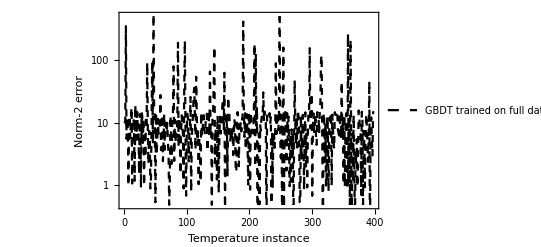
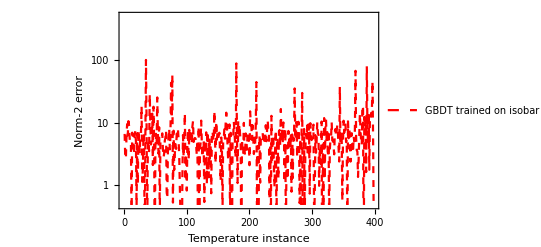
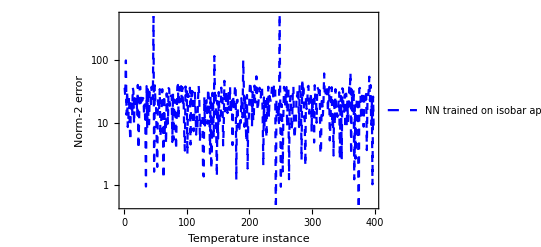

```mathematica
(*ListLogPlot[Abs[{errOverall[[All,1]]*100/mldata1[[i,2]], errOverall[[All,2]], errOverall[[All,3]]}],Frame->True,PlotRange->{All,All},FrameStyle->Black,FrameLabel->{"Temperature instance","Error in kJ/kg"},PlotStyle->{{Dashed,Black},{Dashed, Red},{Dashed, Blue}},PlotLegends->{"Full data, GBDT","Isobar, GBDT","NN with \nnaive percepteron"},Joined->True]*)

{ListLogPlot[Abs[{errOverall[[All,1]]}],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,500}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Black}},PlotLegends->{"GBDT trained on full data \napplied to isobar"},Joined->True],

ListLogPlot[Abs[{errOverall[[All,2]]}],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,500}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed, Red}},PlotLegends->{"GBDT trained on isobar \napplied to isobar"},Joined->True],

ListLogPlot[Abs[{errOverall[[All,3]]}],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,500}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed, Blue}},PlotLegends->{"NN trained on isobar \napplied to isobar"},Joined->True]}
```

## Neural network applied to complete dataset

```mathematica
s2=Dimensions[mldata][[1]];
mldata3=Table[mldata[[i,1]]->{mldata[[i,2]]},{i,1,s2,1}];
training2=mldata3[[1;;Ceiling[s2];;All]];
```

```mathematica
NNAllData=NetTrain[net,mldata3]
```

NetChain[<>]

```mathematica
Norm2[GroundTruth_, PredictionObject_]:=Module[{gt=GroundTruth, po=PredictionObject},
SeedRandom[1234];
Table[Abs[Norm[gt[[i,2]]-po[gt[[i,1]]],"Frobenius"]],{i,1,Length[gt],1}] (*gt is in the form {T,P}->h*)
]
```

```mathematica
(*errNorm1=Table[{
Norm[mldata3[[i,2]]-pThermo1[mldata3[[i]][[1]]],"Frobenius"],
Norm[mldata3[[i,2]]-NNAllData[mldata3[[i]][[1]]],"Frobenius"]},{i,1,Dimensions[mldata3][[1]],100}];*)
```

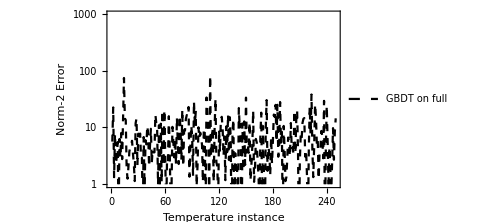
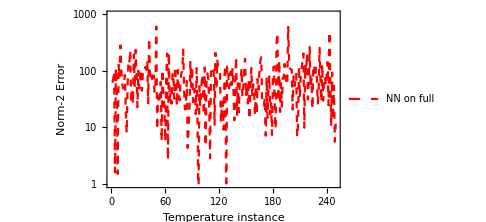

```mathematica
{ListLogPlot[Norm2[RandomSample[mldata3,250],pThermo1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,1000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 Error"},PlotStyle->{{Dashed,Black}},PlotLegends->{"GBDT on full"},Joined->True,ImageSize->Medium],

ListLogPlot[Norm2[RandomSample[mldata3,250],NNAllData],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,1000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 Error"},PlotStyle->{{Dashed, Red}},PlotLegends->{"NN on full"},Joined->True,ImageSize->Medium]}
```

```mathematica
{Mean[Norm2[RandomSample[mldata3,250],pThermo1]],Median[Norm2[RandomSample[mldata3,250],pThermo1]]}
```

{11.6064,5.18219}

```mathematica
{Mean[Norm2[RandomSample[mldata3,250],NNAllData]],Median[Norm2[RandomSample[mldata3,250],NNAllData]]}
```

{57.7158,38.4777}

## Partition of data based on region leads to better prediction

```mathematica
zone1Selection=Select[dataset, #[[3]]== 1&];
```

```mathematica
t1=Table[zone1Selection[[i]][[1]],{i,1,Length[zone1],1}];
p1=Table[zone1Selection[[i]][[2]],{i,1,Length[zone1],1}];
hz1=Table[zone1Selection[[i]][[4]],{i,1,Length[zone1],1}];
```

```mathematica
SeedRandom[1234];
zone1Data=
Thread[
RandomSample[Table[
{t1[[i]],p1[[i]]}->{hz1[[i]]},{i,1,Length[zone1Selection],1}]]
];
```

```mathematica
zone1Training=Take[zone1Data,Ceiling[0.7*Length[zone1Selection]]];
zone1Validation=Take[zone1Data,-Ceiling[0.3*Length[zone1Selection]]];
```

```mathematica
nnz1=NetTrain[net,zone1Training]
```

NetChain[<>]

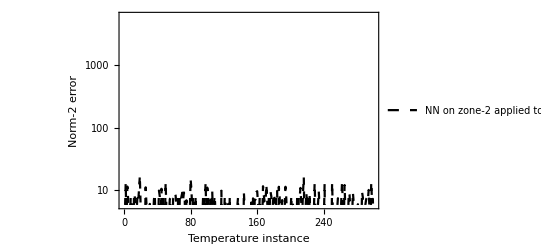
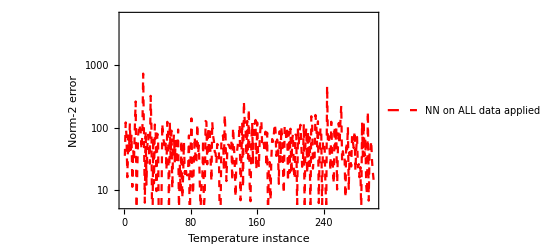
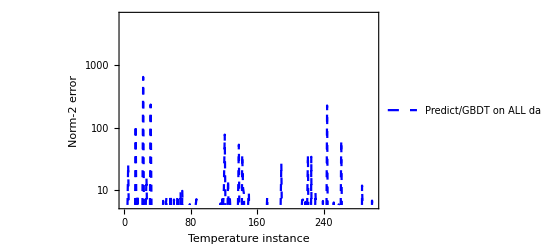

```mathematica
n=300;
{ListLogPlot[Norm2[RandomSample[zone1Validation,n],nnz1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Black}},PlotLegends->{"NN on zone-2\napplied to zone-2"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone1Validation,n],NNAllData],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Red}},PlotLegends->{"NN on ALL data\napplied to zone-2"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone1Validation,n],pThermo1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Blue}},PlotLegends->{"Predict/GBDT on ALL data\napplied to zone-2"},Joined->True]

}
```

## Partition of data based on region (zone) leads to better prediction

```mathematica
ZoneData[zoneNum_]:= Module[{znum=zoneNum},
zoneSelection=Select[dataset, #[[3]]== znum&];
tz=Table[zoneSelection[[i]][[1]],{i,1,Length[zoneSelection],1}];
pz=Table[zoneSelection[[i]][[2]],{i,1,Length[zoneSelection],1}];
hz=Table[zoneSelection[[i]][[4]],{i,1,Length[zoneSelection],1}];
SeedRandom[1234];
Thread[
RandomSample[Table[
{tz[[i]],pz[[i]]}->{hz[[i]]},{i,1,Length[zoneSelection],1}]]
]
]
```

```mathematica
zone2Data=ZoneData[2];
zone2Training=Take[zone2Data,Ceiling[0.7*Length[zone2Data]]];
zone2Validation=Take[zone2Data,-Ceiling[0.3Length[zone2Data]]];
Length[zone2Training]
```

9537

```mathematica
net2=NetChain[{
32,Tanh,32,8,1},
"Input"->2];
nnz2=NetTrain[net,zone2Training]
```

NetChain[<>]

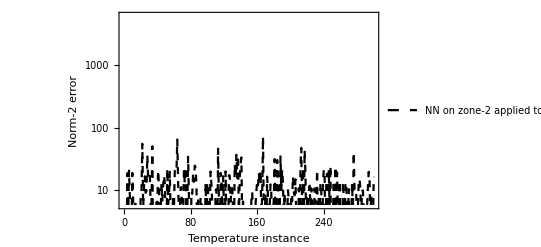
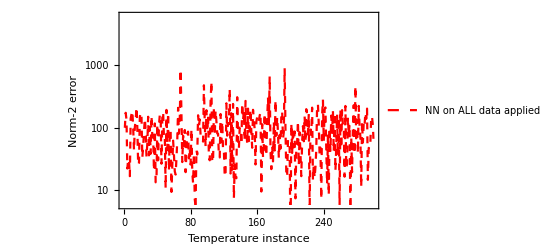
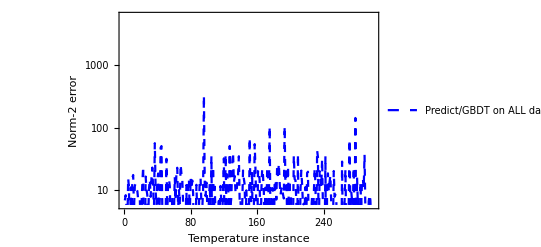

```mathematica
n=300;
{ListLogPlot[Norm2[RandomSample[zone2Validation,n],nnz2],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Black}},PlotLegends->{"NN on zone-2\napplied to zone-2"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone2Validation,n],NNAllData],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Red}},PlotLegends->{"NN on ALL data\napplied to zone-2"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone2Validation,n],pThermo1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Blue}},PlotLegends->{"Predict/GBDT on ALL data\napplied to zone-2"},Joined->True]

}
```

## C̶o̶n̶c̶l̶u̶s̶i̶o̶n̶s̶ Summary

Water/Steam enthalpy data available from the IF-97 industrial standard is used to train predictive models.

The Predict/GBDT and a Naive percepteron neural network (NPNN) model are both trained on the ~95% of data-set.  The Predict/GBDT has a better prediction than the NPNN model.

The full dataset is partitioned into 4 zones per the IF-97 standard.  The NPNN is trained on these 2 zones (NPNN-zones).  Not only is this training process faster, the predictions made by the NPNN-zones is better on the partitioned zones than the Predict/GBDT and the NPNN models from the full dataset.

Overall: it is advantageous to partition enthalpy data for speed and accuracy, even with the most Naive of percepterons.

## Extra Data

```mathematica
supHeat={{150,0.1}, {200,0.1},{300,0.1}, {400,0.1},
{250,2},{300,2},{350,2},{400,2},
{250,10},{300,10}, {350,10},{400,10},
{325,100},{375,100},{400,100},{450,100},
{250,400},{300,400},{350,400},{400,400}
};
subcooled={
{50,50},{100,50},
{50,100}, {100,100}
};
```

```mathematica
errRelief=Table[Flatten[Join[{wpe1[[i]][[1]],Abs[err[[i]]]}]],{i,1,30,1}];
ListPlot3D[errRelief,InterpolationOrder->0,Mesh->None,Filling->Bottom,ColorFunction->"TemperatureMap",PlotRange->{{0,2000},{0,1000},{0,100}},AxesLabel->{"Temperature [C]","Pressure [bar]","%Error"},PlotLegends->Automatic,PlotLabel->"Error Plot (>10%)"]//Inactivate;
```

```mathematica
Show[
ListPointPlot3D[{{99,1,100},{205,17,100},{250,40,100},{300,85,100},{325,120,100},{350,165,100}},PlotStyle->{Red,PointSize->0.03},PlotRange->{{0,2000},{0,1000},{0,100}}],ListPlot3D[{errRelief},InterpolationOrder->0,Mesh->None,Filling->Bottom,ColorFunction->"TemperatureMap",PlotRange->{{0,2000},{0,1000},{0,100}},AxesLabel->{"Temperature [C]","Pressure [bar]","%Error"},PlotLegends->Automatic,PlotLabel->"Error Plot (>10%)"]];
```

```mathematica
(*Switch off some messages*)
Off[NDSolve::mxsst]; 
Off[NDSolve::ibcinc]; 
Off[NDSolve::eerr]; 
Off[NDSolve::ndsz]; 
pbcs={ Derivative[0, 1][u][t, xMin] == Derivative[0, 1][u][t, xMax], 
      Derivative[0, 2][u][t, xMin] == Derivative[0, 2][u][t, xMax], 
      Derivative[0, 3][u][t, xMin] == Derivative[0, 3][u][t, xMax], 
      u[t, xMin] == u[t, xMax]};
met={ MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}};
```

## ‘Hello World’ of Classification: Iris Dataset

The Fisher Iris dataset is imported from one of the many online repositories.

```mathematica
url="https://raw.githubusercontent.com/jbrownlee/Datasets/master/iris.csv";
dataset=Import[url];
```

### Probing the dataset to visually ascertain dimensions and identify features

“The dataset contains a set of 150 records under five attributes - petal length, petal width, sepal length, sepal width and species.”

```mathematica
(*names={'sepal-length','sepal-width','petal-length','petal-width','class'}*)
Dimensions[dataset]
dataset[[1;;5]]
dataset[[All,5]]//Tally
```

{150,5}

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa}}

{{Iris-setosa,50},{Iris-versicolor,50},{Iris-virginica,50}}

## Data distribution into bins and Clustering

```mathematica
sepalLength=dataset[[All,1]];
petalLength=dataset[[All,3]];
petalWidth=dataset[[All,4]];
sepalWidth=dataset[[All,2]];
class=dataset[[All,5]]/.{"Iris-setosa"->"setosa", "Iris-versicolor"->"versicolor", "Iris-virginica"->"virginica"};
```

#### Three dimensional/quantitative subsets of data are explored to reveal positive correlation between petal length and petal width

(....as is the well-known case with the Iris dataset)

Clustering method choice is left to the solver.  Further granularity in clustering is possible through choice of specific method such as “Spectral” or “JarvisPatrick”

```mathematica
subset1=Thread[{sepalWidth,petalWidth}];
c1=FindClusters[subset1,Method->"NeighborhoodContraction"];

subset2=Thread[{sepalLength,sepalWidth}];
c2=FindClusters[subset2];

subset3=Thread[{petalLength,petalWidth}];
c3=FindClusters[subset3,Method->"NeighborhoodContraction"]; (*Versus automatic Method*)
```

```mathematica
fr={Frame->True, FrameStyle->Black};
ptstyle={PlotStyle->PointSize[Large]};
```

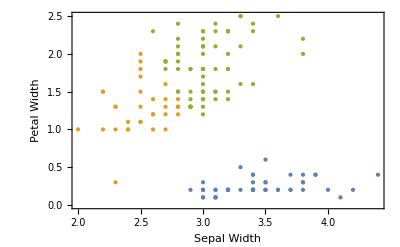
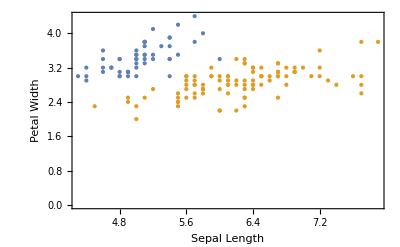
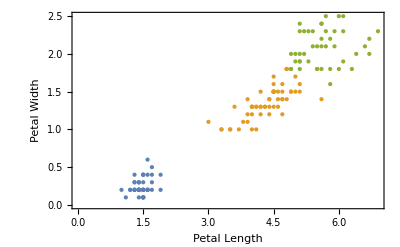

```mathematica
{ListPlot[c1,fr,ptstyle,FrameLabel->{"Sepal Width","Petal Width"}],ListPlot[c2,fr,ptstyle, FrameLabel->{"Sepal Length","Petal Width"}],ListPlot[c3,fr, ptstyle, FrameLabel->{"Petal Length","Petal Width"}]}
```

#### Petal Length and Width show a clean stratification of species class

```mathematica
subset4=Thread[{petalLength,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c4=FindClusters[subset4];

subset5=Thread[{petalWidth,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c5=FindClusters[subset5];
```

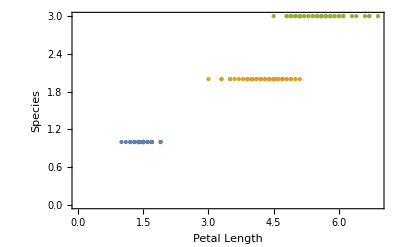
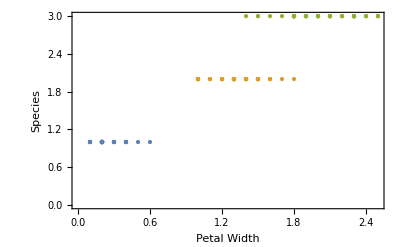

```mathematica
{ListPlot[c4,fr,ptstyle,FrameLabel->{"Petal Length","Species"}],ListPlot[c5,fr,ptstyle,FrameLabel->{"Petal Width","Species"}]}
```

## Classification, Validation and Confusion

For a certain size of training and validation data, the best (minimum speed and accuracy > 93) is  chosen

```mathematica
geomdata=Thread[{sepalLength,sepalWidth,petalLength,petalWidth}];
mldata=RandomSample[Thread[geomdata->class]];
s=Dimensions[mldata][[1]]
training=mldata[[1;;Ceiling[0.8*s]]];
validation=mldata[[Ceiling[0.8*s];;]];
```

150

#### Classification

```mathematica
ciris=Classify[training,PerformanceGoal->"Quality",Method->"DecisionTree"]
```

ClassifierFunction[…]

#### Classifier Measurements

```mathematica
cm=ClassifierMeasurements[ciris,validation]
```

ClassifierMeasurementsObject[…]

#### Accuracy and Confusion Matrix

1.

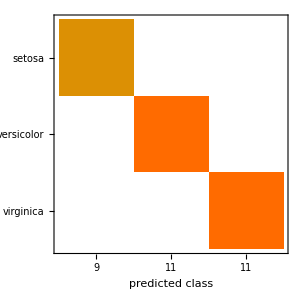

```mathematica
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

## Phase change and Enthalpy jump disconuity

#### Jump in enthalpy for an isobaric process (@1 bar)

```mathematica
(*names={'celcius','bar','region','kJPerKg'}*)
(*s=Dimensions[datasetDirty][[1]];*)
(*dataset=Select[datasetDirty, #[[3]]≠ 0&];*) (*Select only those rows and columns with non zero region*)
(*s=Dimensions[dataset][[1]];*)
Take[dataset,10]
```

{{10,1,1,42.1174},{15,1,1,63.0778},{20,1,1,84.0118},{25,1,1,104.928},{30,1,1,125.833},{35,1,1,146.73},{40,1,1,167.623},{45,1,1,188.516},{50,1,1,209.412},{55,1,1,230.313}}

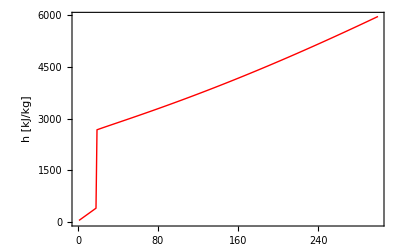

```mathematica
ListLinePlot[dataset[[1;;300,4]],Frame->True,FrameStyle->Black,FrameLabel->{"","h [kJ/kg]"},PlotStyle->{Thick,Red}]
```

```mathematica
start=1;
end=300;
prediction0=Table[pThermo0[{dataset[[i,1]],dataset[[i,2]]}],{i,start,end,1}];
prediction1=Table[pThermo1[{dataset[[i,1]],dataset[[i,2]]}],{i,start, end,1}];
```

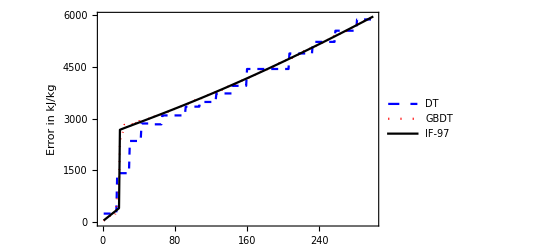

```mathematica
ListLinePlot[{prediction0, prediction1,dataset[[start;;end,4]]},Frame->True,FrameStyle->Black,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dotted,Red},{Thick,Black}},FrameLabel->{"","Error in kJ/kg"},PlotLegends->{"DT","GBDT","IF-97"}]
```

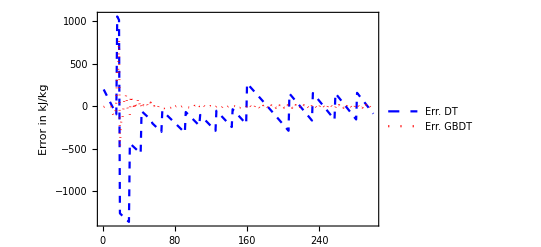

```mathematica
ListLinePlot[{prediction0-dataset[[start;;end,4]], prediction1-dataset[[start;;end,4]]},Frame->True,FrameStyle->Black,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dotted,Red}},FrameLabel->{"","Error in kJ/kg"},PlotLegends->{"Err. DT","Err. GBDT"},PlotRange->{All,All}]
```

## Partitioning of data based on cluster zone prior to NN training

Even with a "naive" percepteron, there is a reduction in the Norm - 2 error measure (or improvement in prediction) by partitioning data based on clustering into zones

```mathematica
SeedRandom[1234];
subset3d=RandomSample[Thread[{P,T,h}]];
c3d=FindClusters[subset3d,4,Method->"KMeans"];ListPlot3D[{c3d[[1]], c3d[[2]], c3d[[3]], c3d[[4]]},Mesh->None, PlotLabel->{"T (C)","P (Bar)","h (kJ/kg)"},PlotLegends->{"zone 1","zone 2","zone 3","zone 4"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
z=1;
t1=Table[c3d[[z]][[i]][[1]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
p1=Table[c3d[[z]][[i]][[2]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
hz1=Table[c3d[[z]][[i]][[3]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
dz1=Length[zone1];
```

```mathematica
SeedRandom[1234];
zone1=
Thread[
RandomSample[Table[
{t1[[i]],p1[[i]]}->{hz1[[i]]},{i,1,Dimensions[t1][[1]],1}]]
];
zone1Training=Take[zone1,Ceiling[0.7*Length[t1]]];
zone1Validation=Take[zone1,-Ceiling[0.3*Length[t1]]];
```

```mathematica
nnz1=NetTrain[net,zone1Training]
```

NetChain[<>]

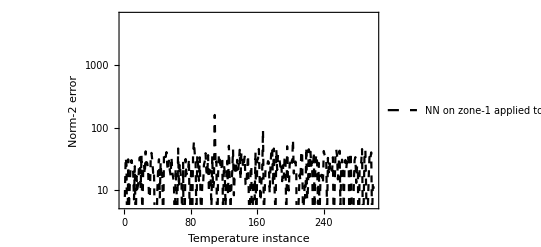
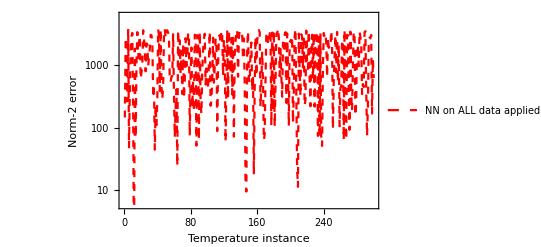
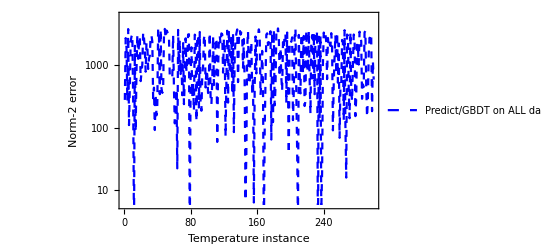

```mathematica
n=300;
{ListLogPlot[Norm2[RandomSample[zone1Validation,n],nnz1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Black}},PlotLegends->{"NN on zone-1\napplied to zone-1"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone1Validation,n],NNAllData],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Red}},PlotLegends->{"NN on ALL data\napplied to zone-1"},Joined->True],

ListLogPlot[Norm2[RandomSample[zone1Validation,n],pThermo1],GridLines->{None,{100}},GridLinesStyle->{RGBColor[.8,.1,1],Thickness[0.02]},Frame->True,PlotRange->{All,{0,6000}},FrameStyle->Black,FrameLabel->{"Temperature instance","Norm-2 error"},PlotStyle->{{Dashed,Blue}},PlotLegends->{"Predict/GBDT on ALL data\napplied to zone-1"},Joined->True]

}
```

```mathematica
{Mean[Norm2[RandomSample[zone1Validation,n],nnz1]],Median[Norm2[RandomSample[zone1Validation,n],nnz1]],StandardDeviation[Norm2[RandomSample[zone1Validation,n],nnz1]]}
```

{10.7312,8.28559,11.2981}

```mathematica
{Mean[Norm2[RandomSample[zone1Validation,n],pThermo1]],Median[Norm2[RandomSample[zone1Validation,n],pThermo1]],StandardDeviation[Norm2[RandomSample[zone1Validation,n],pThermo1]]}
```

{1349.53,813.571,1165.95}

```mathematica
{Mean[Norm2[RandomSample[zone1Validation,n],NNAllData]],Median[Norm2[RandomSample[zone1Validation,n],NNAllData]],StandardDeviation[Norm2[RandomSample[zone1Validation,n],NNAllData]]}
```

{1391.21,999.802,1169.84}